```mathematica
ClearAll["Global`*"]
<<MaTeX`
cm=72/2.54;
```

## System parameter analysis

### Constants

```mathematica
e = Quantity[(1.602176)*10^(-19),"Coulombs"];  (*electron's charge*)
hbar = Quantity[(1.054571)*10^(-34),("Kilograms"*"Meters"^2)/"Seconds"]; (*Plank's constant*)
m= Quantity[(9.109383)*10^(-31),"Kilograms"]; (*electron's mass*)
c = Quantity[(2.997924)*10^(8),"Meters"/"Seconds"]; (*speed of light in vacuum*)
ϵ0 = Quantity[(8.854187)*10^(-12),("Coulombs"^2*"Seconds"^2)/("Kilograms"*"Meters"^(3))]; (*vacuum permittivity*)
eV = Quantity[(1.602176)*10^(-19),("Kilograms"*"Meters"^2)/("Seconds"^(2))];(*electron Volts*)
```

### System parameters

```mathematica
B = Quantity[(1.2),"Kilograms"/("Coulombs"*"Seconds")]; (*Stationary magnetic field's amplitude = 1.2 T*)
ElecInt0= Quantity[(1)*10^(6),"Kilograms"/"Seconds"^(3)]; (*Reference dressing electric field's intensity = 100 Wcm^-2*)
ω = Quantity[(2)*10^(12),"Seconds"^(-1)]; (*Dressing field's frequency = 2×10^12 rads^-1*)
me = 0.071*m;  (*Effective electron's mass for 2DEG = 0.071m*)
```

### Parameter calculation

```mathematica
ω0 = (e*B)/(me);(*cyclotron frequency*) 
E0 = Sqrt[(2*ElecInt0)/(c*ϵ0 )];(*Reference dressing electric field's amplitude*)
b= (e*E0*((ω0 )^2))/(hbar*ω*((ω0 )^2-(ω)^2));(*Pre-defined parameter*)
κ = Sqrt[me*ω0 /hbar]; (*Pre-defined parameter in Gauss-Hermite functions*)
Subscript[λ, 1] = (hbar* b)/(e*B);(*Pre-defined parameter in inverse scattering time*)
Subscript[λ, 2] = (hbar *κ )/(e*B); (*Pre-defined parameter in inverse scattering time*)
```

### Parameter values

```mathematica
k0 =Quantity[1*10^(8),"Meters"^(-1)];
```

```mathematica
λ1 = NumberForm[Subscript[λ, 1]*k0,4]
```

(280.5 (1.602×10^-19 C)^2 (1.2 kg/(s C)) (100000000 per meter) √((1000000 kg/s^3)/((8.854×10^-12 s^2 C^2/(kg m^3)) (2.998×10^8 m/s))))/((9.109×10^-31 kg)^2 (2000000000000 per second) ((198.4 (1.602×10^-19 C)^2 (1.2 kg/(s C))^2)/((9.109×10^-31 kg)^2)-(2000000000000 per second)^2))

```mathematica
λ2 = NumberForm[Subscript[λ, 2]*k0,4]
```

(1. (1.055×10^-34 kg m^2/s) √(((1.602×10^-19 C) (1.2 kg/(s C)))/(1.055×10^-34 kg m^2/s)) (100000000 per meter))/((1.602×10^-19 C) (1.2 kg/(s C)))

## Landau level wavefunction χ_N

```mathematica
χ[y_?NumericQ,N_?NumericQ]:= Exp[-y^2/2]/(√(2^N*N!*√π))HermiteH[N,y];
```

We can define normalized dressed electric field intensity = ElecInt := (Real electric field intensity)/ElecInt0 where ElecInt0 =  100 Wcm^-2.

## Inverse scattering time matrix central element analysis (l=0)

### Landau level N=0

```mathematica
Q0:= χ[2.342*k2,0]*χ[2.342*(k1-k2),0];
A0[k1_?NumericQ,ElecInt_?NumericQ]:=((BesselJ[0,2.090*Sqrt[ElecInt]*(k1)])^2)*((NIntegrate[Q0,{k2,-Infinity,Infinity},AccuracyGoal->4])^2);
Sup0 := NIntegrate[A0[k1,e],{k1,-Infinity,Infinity},AccuracyGoal->4];
Sdown0:= NIntegrate[A0[k1,0],{k1,-Infinity,Infinity},AccuracyGoal->4];
Tinverse0 := Sup0/Sdown0;
```

### Landau level N=1

```mathematica
Q1:= χ[2.342*k2,1]*χ[2.342*(k1-k2),1];
A1[k1_?NumericQ,ElecInt_?NumericQ]:=((BesselJ[0,2.090*Sqrt[ElecInt]*(k1)])^2)*((NIntegrate[Q1,{k2,-Infinity,Infinity},AccuracyGoal->4])^2);
Sup1:= NIntegrate[A1[k1,e],{k1,-Infinity,Infinity},AccuracyGoal->4];
Sdown1:= NIntegrate[A0[k1,0],{k1,-Infinity,Infinity},AccuracyGoal->4];
Tinverse1 := Sup1/Sdown1;
```

### Landau level N=2

```mathematica
Q2:= χ[2.342*k2,2]*χ[2.342*(k1-k2),2];
A2[k1_?NumericQ,ElecInt_?NumericQ]:=((BesselJ[0,2.090*Sqrt[ElecInt]*(k1)])^2)*((NIntegrate[Q2,{k2,-Infinity,Infinity},AccuracyGoal->4])^2);
Sup2:= NIntegrate[A2[k1,e],{k1,-Infinity,Infinity},AccuracyGoal->4];
Sdown2:= NIntegrate[A0[k1,0],{k1,-Infinity,Infinity},AccuracyGoal->4];
Tinverse2 := Sup2/Sdown2;
```

### Landau level N=3

```mathematica
Q3:= χ[2.342*k2,3]*χ[2.342*(k1-k2),3];
A3[k1_?NumericQ,ElecInt_?NumericQ]:=((BesselJ[0,2.090*Sqrt[ElecInt]*(k1)])^2)*((NIntegrate[Q3,{k2,-Infinity,Infinity},AccuracyGoal->4])^2);
Sup3:= NIntegrate[A3[k1,e],{k1,-Infinity,Infinity},AccuracyGoal->4];
Sdown3:= NIntegrate[A0[k1,0],{k1,-Infinity,Infinity},AccuracyGoal->4];
Tinverse3:= Sup3/Sdown3;
```

### Landau level N=4

```mathematica
Q4:= χ[2.342*k2,4]*χ[2.342*(k1-k2),4];
A4[k1_?NumericQ,ElecInt_?NumericQ]:=((BesselJ[0,2.090*Sqrt[ElecInt]*(k1)])^2)*((NIntegrate[Q4,{k2,-Infinity,Infinity},AccuracyGoal->4])^2);
Sup4:= NIntegrate[A4[k1,e],{k1,-Infinity,Infinity},AccuracyGoal->4];
Sdown4:= NIntegrate[A0[k1,0],{k1,-Infinity,Infinity},AccuracyGoal->4];
Tinverse4:= Sup4/Sdown4;
```

#### Generating figures

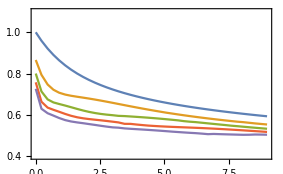

```mathematica
P1=Plot[{Sqrt[Tinverse0],Sqrt[Tinverse1],Sqrt[Tinverse2],Sqrt[Tinverse3],Sqrt[Tinverse4]} ,{e,0,9},
PlotRange->{{0,9},{0.4,1.1}},
PlotLegends->{MaTeX["N=1"],MaTeX["N=2"],MaTeX["N=3"],MaTeX["N=4"],MaTeX["N=5"]},
MaxRecursion->0,
PlotPoints->40,
Axes->False,
Frame->{{True,True},{True,True}},
FrameTicks->{{Automatic,None},{Automatic,None}},
FrameLabel->{{MaTeX["\\Lambda_{N}"],None},{MaTeX["I(100~\\text{W}\\text{cm}^{-2})"],None}},
ImageSize->10*cm]
```

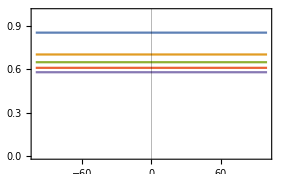

```mathematica
e=1;
P2=Plot[{Sqrt[Tinverse0],Sqrt[Tinverse1],Sqrt[Tinverse2],Sqrt[Tinverse3],Sqrt[Tinverse4]} ,{kx,-100,100},
PlotRange->{{-100,100},{0,1}},
PlotLegends->{MaTeX["N=1"],MaTeX["N=2"],MaTeX["N=3"],MaTeX["N=4"],MaTeX["N=5"]},
GridLines->{{{0,Black}},None},
MaxRecursion->0,
PlotPoints->50,
Axes->False,
Frame->{{True,True},{True,True}},
FrameTicks->{{Automatic,None},{Automatic,None}},
FrameLabel->{{MaTeX["\\Lambda_{N}"],None},{MaTeX["k_x(\\mathring{\\text{A}}^{-1})"],None}},
ImageSize->10*cm]
```

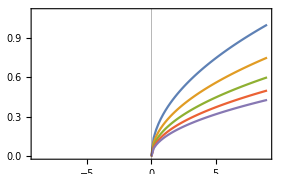

```mathematica
P=Plot[{Sqrt[e]/3,Sqrt[e]/4,Sqrt[e]/5,Sqrt[e]/6,Sqrt[e]/7} ,{e,0,9},
PlotRange->{{-9,9},{0,1.1}},
PlotLegends->{MaTeX["N=1"],MaTeX["N=2"],MaTeX["N=3"],MaTeX["N=4"],MaTeX["N=5"]},
GridLines->{{{0,Black}},None},
MaxRecursion->0,
PlotPoints->50,
Axes->False,
Frame->True,
FrameTicks->{{Automatic,None},{Automatic,None}},
FrameLabel->{{MaTeX["\\Lambda_{N}"],None},{MaTeX["k_x(\\mathring{\\text{A}}^{-1})"],None}},
ImageSize->10*cm]
```

```mathematica
(*Export["nnn.pdf",P1]*)
```

## Manipulate conductivity using dressing field intensity

Normalized conductivity function:

```mathematica
σ[x_,n_,Λ0_,Λ1_] =(n+1)/(0.0037*Λ0*Λ1)* (1/(1+((x-n-1)/(0.06*Λ0))^2))*(1/(1+((x-n)/(0.06*Λ1))^2));
```

Normalized inverse scattering time matrix central element (Λ_N) arrays for different intensity levels:

```mathematica
I0 = List[1.0000,0.8660,0.8004,0.7578,0.7266,0.7021,0.6821,0.6653,0.6507,0.6380,0.6267];
I1 = List[0.8546,0.7037,0.6502,0.6114,0.5810,0.5584,0.5416,0.5280,0.5160,0.5050,0.4948];
I4 = List[0.6875,0.6345,0.5902,0.5528,0.5307,0.5118,0.4958,0.4840,0.4730,0.4629,0.4547];
I9= List[0.5936,0.5539,0.5333,0.5180,0.5006,0.4812,0.4685,0.4564,0.4469,0.4377,0.4305];
I16= List[0.5333,0.4998,0.4824,0.4706,0.4617,0.4543,0.4470,0.4379,0.4274,0.4194,0.4125];
I25= List[0.4899,0.4606,0.4454,0.4350,0.4272,0.4208,0.4155,0.4109,0.4068,0.4029,0.3984];
I49= List[0.4301,0.4061,0.3937,0.3852,0.3787,0.3735,0.3691,0.3654,0.3602,0.3591,0.3564];
```

Getting sum of each Landau level contribution to the conductivity:

```mathematica
For[n=2;t0:=σ[x,0,Extract[I0,1],Extract[I0,2]],n<11,n++,
t0=t0 +σ[x,(n-1),Extract[I0,n],Extract[I0,n+1]]];
For[n=2;t1:=σ[x,0,Extract[I1,1],Extract[I1,2]],n<11,n++,
t1=t1 +σ[x,(n-1),Extract[I1,n],Extract[I1,n+1]]];
For[n=2;t4:=σ[x,0,Extract[I4,1],Extract[I4,2]],n<11,n++,
t4=t4 +σ[x,(n-1),Extract[I4,n],Extract[I4,n+1]]];
For[n=2;t9:=σ[x,0,Extract[I9,1],Extract[I9,2]],n<11,n++,
t9=t9+σ[x,(n-1),Extract[I9,n],Extract[I9,n+1]]];
For[n=2;t16:=σ[x,0,Extract[I16,1],Extract[I16,2]],n<11,n++,
t16=t16+σ[x,(n-1),Extract[I16,n],Extract[I16,n+1]]];
For[n=2;t25:=σ[x,0,Extract[I25,1],Extract[I25,2]],n<11,n++,
t25=t25+σ[x,(n-1),Extract[I25,n],Extract[I25,n+1]]];
For[n=2;t49:=σ[x,0,Extract[I49,1],Extract[I49,2]],n<11,n++,
t49=t49+σ[x,(n-1),Extract[I49,n],Extract[I49,n+1]]];
```

#### Generating figures:

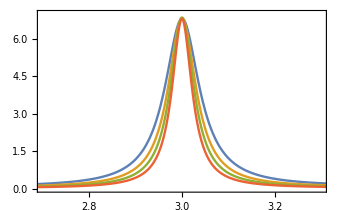

```mathematica
P3 =Plot[{t0,t1,t9,t25},{x,2.5,3.5}, 
PlotLegends->{MaTeX["I=0"],MaTeX["I=I_0"],MaTeX["I=9I_0"],MaTeX["I=25I_0"]},
PlotRange->{{2.7,3.3},{0,7}},
PlotStyle->{Thickness[0.005]},
Axes->False,
Frame->{{True,True},{True,True}},
FrameTicks->{{Automatic,None},{Automatic,None}},
FrameLabel->{{MaTeX["\\sigma^{xx}/\\sigma^{0}"],None},{MaTeX["X_F"],None}},
ImageSize->12*cm]
```

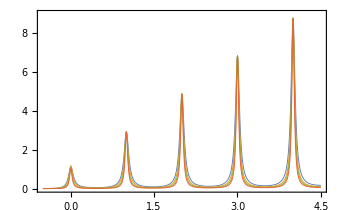

```mathematica
P4 =Plot[{t0,t1,t9,t25},{x,-0.5,4.5}, 
PlotLegends->{MaTeX["I=0"],MaTeX["I=I_0"],MaTeX["I=9I_0"],MaTeX["I=25I_0"]},
PlotRange->{{-0.5,4.5},{0,9}},
PlotStyle->{Thickness[0.002]},
Axes->False,
Frame->{{True,True},{True,True}},
FrameTicks->{{Automatic,None},{Automatic,None}},
FrameLabel->{{MaTeX["\\sigma^{xx}/\\sigma^{0}"],None},{MaTeX["X_F"],None}},
ImageSize->12*cm]
```

```mathematica
Export["fig_1.pdf",-Graphics-];
Export["fig_2.pdf",-Graphics-];
Export["fig_3.pdf",P3];
Export["fig_4.pdf",P4];
```